#### Importing data for Four Oscillators where Oscillator 3 and 4 are entangled and Oscillator 1 and 2 are Not.

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\4 Oscillators with Entanglement Present"];
Dataset1=Table[ReadList["LNData_NM_beta_0.3_Oomega_"<>ToString[file]<>"_Generate-Preserve_Entanglement.txt"], {file, 1., 2., 0.05}];
```

#### Importing data for just Two Oscillators where Oscillator 1 and 2 are NOT entangled.

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\JUST 2 Oscillators Vacuum States"];
Dataset2=Table[ReadList["LNData_NM_beta_0.3_Oomega_"<>ToString[file]<>"_Generating_Entanglement_Just12.txt"], {file, 1., 2., 0.05}];
```

#### Importing data for just Two Oscillators where Oscillator 3 and 4 are entangled.

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\JUST 2 Oscillators Two Mode Squeezed State"];
Dataset3=Table[ReadList["LNData_NM_beta_0.3_Oomega_"<>ToString[file]<>"_Generating_Entanglement_Just34.txt"], {file, 1., 2., 0.05}];
```

```mathematica
height=400;
width=1000;
PlotFormat1={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"τ", "𝒩"}, AxesStyle->Directive[Black, 23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 25], PlotRange->All};

GeneratingEntanglementLeft=ListLinePlot[{Dataset1[[1]][[6]][[1;;401]], Dataset3[[1]][[1;;401]], Dataset1[[1]][[1]][[1;;401]], Dataset2[[1]][[1;;401]]}, PlotRange->{0,3}, Evaluate[PlotFormat1], PlotStyle->{ Directive[Red], Directive[Orange], Directive[Blue], Directive[Purple]}];
GeneratingEntanglementLeft2=ListLinePlot[{Dataset1[[21]][[6]][[1;;401]], Dataset3[[21]][[1;;401]], Dataset1[[21]][[1]][[1;;401]], Dataset2[[21]][[1;;401]]}, PlotRange->{0,3}, Evaluate[PlotFormat1], PlotStyle->{ Directive[Red, Dashed], Directive[Orange, Dashed], Directive[Blue, Dashed], Directive[Purple, Dashed]}];
LEFTPlot=Rasterize[Show[GeneratingEntanglementLeft, GeneratingEntanglementLeft2]]
```

-Graphics-

```mathematica
Dataset2[[21]][[380;;401]]
```

{{189.5,0.478984},{190.,0.475818},{190.5,0.478048},{191.,0.479361},{191.5,0.476045},{192.,0.477497},{192.5,0.479607},{193.,0.476405},{193.5,0.476963},{194.,0.479705},{194.5,0.476871},{195.,0.47649},{195.5,0.479645},{196.,0.477405},{196.5,0.476117},{197.,0.479434},{197.5,0.477965},{198.,0.475872},{198.5,0.479089},{199.,0.478507},{199.5,0.475777},{200.,0.478636}}

```mathematica
Manipulate[ListLinePlot[{Dataset1[[file]][[6]][[1;;401]], Dataset3[[file]][[1;;401]]}, ImageSize->Medium, PlotRange->{1.3, 3}, PlotLegends->{"Oscillator 3,4 with 1,2 Present", "Oscillator 3,4 Only"}, PlotStyle->{Directive[Red], Directive[Orange]}], {file, 1, 21, 1}];

Manipulate[ListLinePlot[{Dataset1[[file]][[1]][[1;;401]], Dataset2[[file]][[1;;401]]}, ImageSize->Medium, PlotRange->{0, 0.6}, PlotLegends->{"Oscillator 1,2 with 3,4 Present", "Oscillator 1,2 Only"}, PlotStyle->{Directive[Blue], Directive[Purple]}], {file, 1, 21, 1}];

Manipulate[ListLinePlot[{Dataset1[[file]][[6]][[1;;401]], Dataset3[[file]][[1;;401]], Dataset1[[file]][[1]][[1;;401]], Dataset2[[file]][[1;;401]]}, ImageSize->Large, Evaluate[PlotFormat1], PlotLegends->Placed[{"Oscillator 3,4 with 1,2 Present", "Oscillator 3,4 Only", "Oscillator 1,2 with 3,4 Present", "Oscillator 1,2 Only"},{Bottom, Right}], PlotStyle->{ Directive[Red], Directive[Orange], Directive[Blue], Directive[Purple]}, AspectRatio->1], {file, 1, 21, 1}, ControlPlacement->Top]
```

```mathematica
MVOscillator34with12=Table[{1+(file-1)*0.05, Mean[Table[Dataset1[[file]][[6]][[pt]][[2]], {pt, 165, 401}]]}, {file, 1, 21}];
MVOscillator12with34=Table[{1+(file-1)*0.05, Mean[Table[Dataset1[[file]][[1]][[pt]][[2]], {pt, 165, 401}]]}, {file, 1, 21}];
MVOscillatorJUST34=Table[{1+(file-1)*0.05, Mean[Table[Dataset3[[file]][[pt]][[2]], {pt, 165, Length[Dataset2[[1]]]}]]}, {file, 1, 21}];
MVOscillatorJUST12=Table[{1+(file-1)*0.05, Mean[Table[Dataset2[[file]][[pt]][[2]], {pt, 165, Length[Dataset2[[1]]]}]]}, {file, 1, 21}];
```

```mathematica
height=400;
width=600;
PlotFormat2={ImageSize->{UpTo[width], UpTo[height]}, AspectRatio->height/width,  AxesLabel->{"Ω=ω", "𝒩"}, AxesStyle->Directive[Black, 23], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 25], PlotRange->All, PlotStyle->Thickness[0.0010]};
```

```mathematica
RIGHTPlot=Rasterize[Show[ListLinePlot[{MVOscillator34with12, MVOscillatorJUST34, MVOscillator12with34, MVOscillatorJUST12},PlotStyle->{ Directive[Red], Directive[Orange], Directive[Blue], Directive[Purple]}, PlotRange->{0, 3}, Evaluate[PlotFormat2]],ListPlot[{MVOscillator34with12, MVOscillatorJUST34, MVOscillator12with34, MVOscillatorJUST12},PlotStyle->{ Directive[Red, PointSize->0.015], Directive[Orange, PointSize->0.015], Directive[Blue, PointSize->0.015], Directive[Purple, PointSize->0.015]}, Evaluate[PlotFormat2]]]]
```

-Graphics-

```mathematica
GeneratingEntanglement=Rasterize[GraphicsRow[{LEFTPlot, RIGHTPlot}], ImageSize->Full]
```

-Graphics-

```mathematica
SetDirectory["C:\\Users\\physk\\OneDrive\\Desktop\\Generate Entanglement"]
Export["GeneratingEntanglement.png", GeneratingEntanglement]
```

C:\Users\physk\OneDrive\Desktop\Generate Entanglement

GeneratingEntanglement.png

```mathematica
(* Purple *)
(* MVOscillatorJUST12[[1]] *)

(* Blue *)
MeanDataBlue=Table[ MVOscillator12with34[[Omega]][[2]], {Omega, 1, 21}];
(* Purple *)
MeanDataPurple=Table[ MVOscillatorJUST12[[Omega]][[2]], {Omega, 1, 21}];
```

```mathematica
(* MeanData from Generating Entanglement with zero initial Entanglement in 4 Oscillator System, Figure 10 *)
MeanDataFigure10={0,0,0.00358342,0.0182832,0.0352982,0.0511245,0.0658623,0.0796022,0.0924385,0.104466,0.115769,0.12641,0.136437,0.145899,0.154854,0.16335,0.171418,0.179082,0.186369,0.193314,0.199946};
```

```mathematica
(* Omega Values *)
OmegaValues=Table[Omega, {Omega, 1, 2, 0.05}];
```

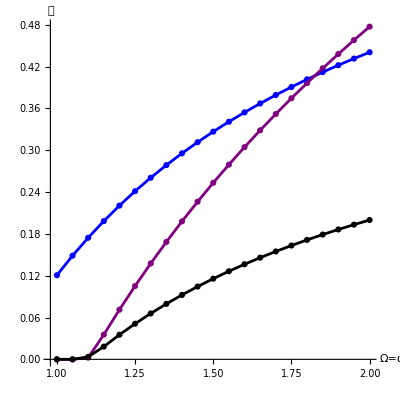
Omega
(1.
1.05
1.1
1.15
1.2
1.25
1.3
1.35
1.4
1.45
1.5
1.55
1.6
1.65
1.7
1.75
1.8
1.85
1.9
1.95
2.)    Blue
(0.120704
0.148779
0.174462
0.198384
0.220683
0.24134
0.26062
0.27872
0.295681
0.31165
0.326761
0.34101
0.35445
0.367211
0.379342
0.390851
0.4018
0.41223
0.422153
0.431617
0.440668)    Purple
(0
0
0.00244964
0.0354476
0.071258
0.105256
0.137615
0.168489
0.197995
0.226255
0.253378
0.279447
0.304541
0.328736
0.352095
0.37467
0.396515
0.417677
0.438195
0.458105
0.477446)    Pastel
(0
0
0.00358342
0.0182832
0.0352982
0.0511245
0.0658623
0.0796022
0.0924385
0.104466
0.115769
0.12641
0.136437
0.145899
0.154854
0.16335
0.171418
0.179082
0.186369
0.193314
0.199946)-Graphics-

```mathematica
DataComparisonGraph=Show[{
ListPlot[{MVOscillator12with34, MVOscillatorJUST12, Table[{MVOscillatorJUST12[[Omega]][[1]], MeanDataFigure10[[Omega]]}, {Omega, 1, 21}]}, PlotStyle->{Directive[Blue], Directive[Purple], Directive[Black]}, AspectRatio->1,  AxesLabel->{"Ω=ω", "𝒩"}, AxesStyle->Directive[Black, 18], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 18],ImageSize->{400, 400}], 

ListLinePlot[{MVOscillator12with34, MVOscillatorJUST12, Table[{MVOscillatorJUST12[[Omega]][[1]], MeanDataFigure10[[Omega]]}, {Omega, 1, 21}]}, PlotStyle->{Directive[Blue], Directive[Purple], Directive[Black]}, AspectRatio->1,  AxesLabel->{"Ω=ω", "𝒩"}, AxesStyle->Directive[Black, 18], BaseStyle->{FontFamily->"Latin Modern Roman"},  LabelStyle->Directive[Black, 18],ImageSize->{400, 400}]}];
Row[{Column[{" Omega", OmegaValues//MatrixForm}], Column[{"    Blue", MeanDataBlue//MatrixForm}], Column[{"    Purple", MeanDataPurple//MatrixForm}], Column[{"    Pastel", MeanDataFigure10//MatrixForm}], DataComparisonGraph}]
```

```mathematica
Table[OmegaValues[[value]], {value, 6, 21, 5}]
(* Blue *)
Table[MeanDataBlue[[value]], {value, 6, 21, 5}]
(* Purple *)
Table[MeanDataPurple[[value]], {value, 6, 21, 5}]
(* Pastel *)
Table[MeanDataFigure10[[value]], {value, 6, 21, 5}]
```

{1.25,1.5,1.75,2.}

{0.24134,0.326761,0.390851,0.440668}

{0.105256,0.253378,0.37467,0.477446}

{0.0511245,0.115769,0.16335,0.199946}

```mathematica
MV34with12func=NonlinearModelFit[MVOscillator34with12, a*x^2+b*x+c, {a, b, c}, x];
MV12with34func=NonlinearModelFit[MVOscillator12with34, a*x^2+b*x+c, {a, b, c}, x];
Row[{Column[{"Oscillator 34 with 12", MV34with12func[{"ParameterTable"}], MV34with12func}],
Column[{"Oscillator 12 with 34", MV12with34func[{"ParameterTable"}], MV12with34func}]}]

MV34func=NonlinearModelFit[MVOscillatorJUST34, a*x^2+b*x+c, {a, b, c}, x];
MV12func=NonlinearModelFit[MVOscillatorJUST12[[3;;21]], a*x^2+b*x+c, {a, b, c}, x];
Row[{Column[{"Oscillator 34", MV34func[{"ParameterTable"}], MV34func}],
Column[{"Oscillator 12", MV12func[{"ParameterTable"}], MV12func}]}]
```

Oscillator 34 with 12
{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.177746 | 0.00725435 | -24.502 | 2.82093×10^-15
b | 0.846498 | 0.0218509 | 38.7397 | 8.60299×10^-19
c | 0.900417 | 0.0159413 | 56.4831 | 1.02399×10^-21}
FittedModel[…]Oscillator 12 with 34
{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.182972 | 0.00698374 | -26.1997 | 8.71501×10^-16
b | 0.859179 | 0.0210358 | 40.8436 | 3.35455×10^-19
c | -0.549876 | 0.0153467 | -35.8303 | 3.44765×10^-18}
FittedModel[…]

Oscillator 34
{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.227847 | 0.00818937 | -27.8223 | 3.02898×10^-16
b | 1.23602 | 0.0246673 | 50.1077 | 8.72821×10^-21
c | 0.355198 | 0.0179961 | 19.7376 | 1.20976×10^-13}
FittedModel[…]Oscillator 12
{ | Estimate | Standard Error | t-Statistic | P-Value
a | -0.198936 | 0.00511794 | -38.8703 | 2.86816×10^-17
b | 1.14081 | 0.0159147 | 71.6827 | 1.69523×10^-21
c | -1.01088 | 0.012073 | -83.7308 | 1.42042×10^-22}
FittedModel[…]

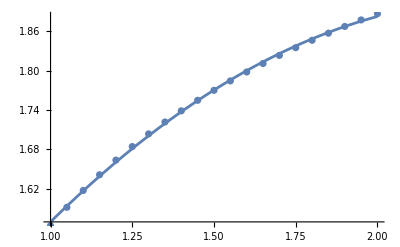

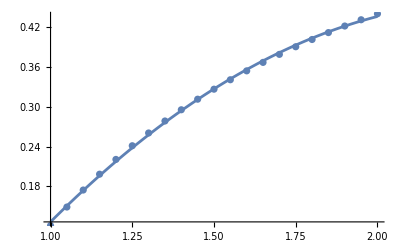

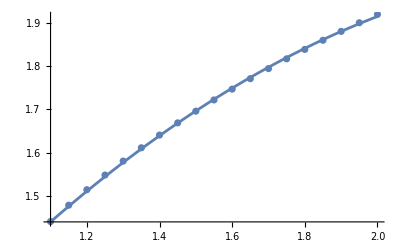

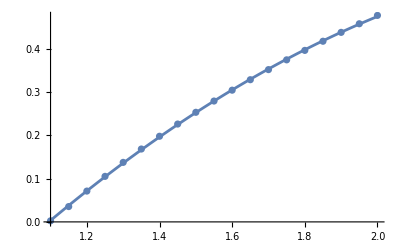

```mathematica
Show[{Plot[{MV34with12func[x]}, {x, 1, 2}],ListPlot[MVOscillator34with12]}]
Show[{Plot[{MV12with34func[x]}, {x, 1, 2}],ListPlot[MVOscillator12with34]}]
Show[{Plot[{MV34func[x]}, {x, 1.1, 2}],ListPlot[MVOscillatorJUST34]}]
Show[{Plot[{MV12func[x]}, {x, 1.1, 2}],ListPlot[MVOscillatorJUST12]}]
```

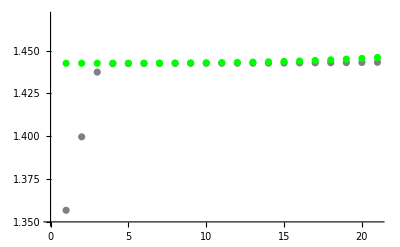

```mathematica
EntanglementDifference4Osc=Table[{file, Mean[Table[Dataset1[[file]][[6]][[pt]][[2]]-Dataset1[[file]][[1]][[pt]][[2]], {pt, 165, 401}]]}, {file, 1, 21}];
EntanglementDifference2Osc=Table[{file, Mean[Table[Dataset3[[file]][[pt]][[2]]-Dataset2[[file]][[pt]][[2]], {pt, 165, Length[Dataset2[[1]]]}]]}, {file, 1, 21}];
ListPlot[{EntanglementDifference2Osc, EntanglementDifference4Osc}, PlotRange->{1.35, 1.47}, PlotStyle->{Directive[Gray], Directive[Green]}]
```

```mathematica
Meandiffvalue4osc=Mean[Table[EntanglementDifference4Osc[[file]][[2]], {file, 1, 21}]];
Maxdiffvalue4osc=EntanglementDifference4Osc[[21]][[2]];
Mindiffvalue4osc=EntanglementDifference4Osc[[1]][[2]];
```

```mathematica
plusamount1=Maxdiffvalue4osc-Meandiffvalue4osc;
minusamount1=Meandiffvalue4osc-Mindiffvalue4osc;
Around[Meandiffvalue4osc, {minusamount1, plusamount1}]
```

1.44350.00090.0025

```mathematica
Meandiffvalue2osc=Mean[Table[EntanglementDifference2Osc[[file]][[2]], {file, 1, 21}]];
Maxdiffvalue2osc=EntanglementDifference2Osc[[21]][[2]];
Mindiffvalue2osc=EntanglementDifference2Osc[[1]][[2]];
```

```mathematica
plusamount2=Maxdiffvalue2osc-Meandiffvalue2osc;
minusamount2=Meandiffvalue2osc-Mindiffvalue2osc;
Around[Meandiffvalue2osc, {minusamount2, plusamount2}]
```

1.4360.080.007

```mathematica
PercentDiff[value1_, value2_]:=Abs[value1-value2]/Mean[{value1, value2}]*100
PercentDiff[Meandiffvalue4osc, Meandiffvalue2osc]
```

0.49514

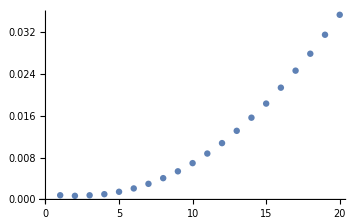
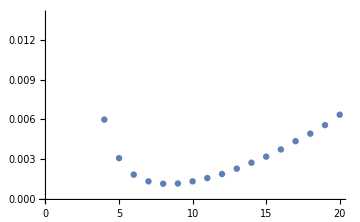

```mathematica
Row[{
ListPlot[Table[PercentDiff[EntanglementDifference4Osc[[file]][[2]], EntanglementDifference4Osc[[file+1]][[2]]], {file, 1, 20}], ImageSize->Medium],
ListPlot[Table[PercentDiff[EntanglementDifference2Osc[[file]][[2]], EntanglementDifference2Osc[[file+1]][[2]]], {file, 1, 20}], ImageSize->Medium]}]
```